```mathematica
FactorInteger[8133007150]
```

{{2,1},{5,2},{162660143,1}}

```mathematica
FactorInteger[9177511682]
```

{{2,1},{47,1},{193,1},{505871,1}}

```mathematica
FactorInteger[3015359717]
```

{{17,1},{19,2},{491341,1}}

```mathematica
ω[n_]:=Length[FactorInteger[n]]
```

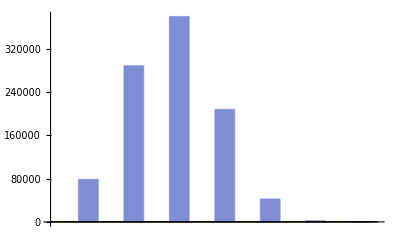

```mathematica
BarChart[Tally[Table[ω[x],{x,1,10^6}]]]
```

```mathematica
N[Log[Log[10^6]]]
```

2.62579